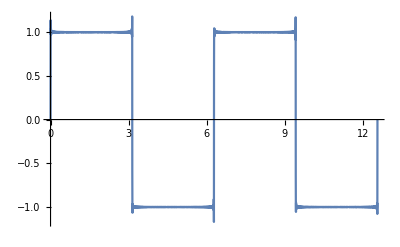

```mathematica
f=0;
Do[f+={4/Pi}{1/n}Sin[n t],{n, 1, 1000, 2}];
f;
Plot[f,{t, 0, 4 Pi}]
```

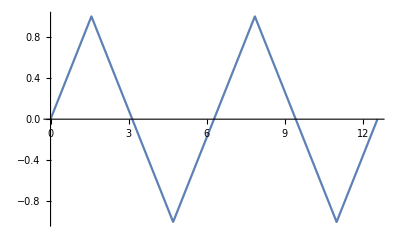

```mathematica
f=0;
Do[f+={8/Pi^2}{{-1}^{{n-1}/2}/n^2}Sin[n t],{n, 1, 1000, 2}];
f;
Plot[f,{t, 0, 4 Pi}]
```

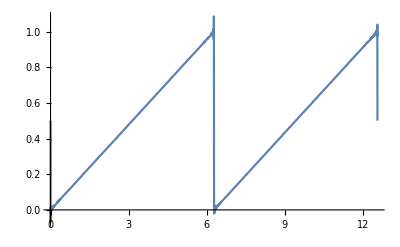

```mathematica
f={1/2};
Do[f-={1/Pi}{1/n }Sin[n t],{n, 1, 1000, 1}];
f;
Plot[f,{t, 0, 4 Pi}]
```